# Practical 11

### Submitted By- Puranjyoti Bera (20201043)

Show that ∫_C_1 zⅆz = ∫_C_2 zⅆz = 4 + 2i where C_1is the line segment from -1 - i to 3 + i and C_2is the portion of the parabola 
x = y^2+2y joining -1 - i to 3 + i. Make plots of two contours C_1 and C_2 joining -1 - i to 3 + i.

The parameterization of the line segment C_1 is given by

C_1:z(t)=2+ⅇ^(ⅈ t), 0≤t≤1

The parametrization of the portion of the parabola C_2is given by

C_2:z(t)=(2+ⅈ) t+t^2, -1≤t≤1

The plots of the line segment  C_(1\n) and the portion of the parabola  C_2 are given by the figure

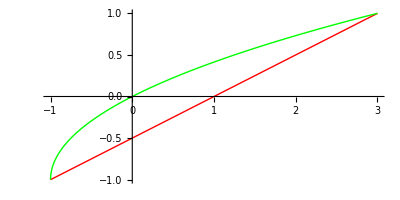

∫_C_1 zⅆz = 4+2 ⅈ

∫_C_2 zⅆz = 4+2 ⅈ

```mathematica
w1:=-1-I;
w2:=3+I;
z1[t_]:=(1-t)*w1+t*w2;
z2[t_]:=(t^2+2*t)+I*t;
Print["The parameterization of the line segment C_1 is given by"];
Print["C_1:z(t)=",z[t],", 0≤t≤1"]; 
Print["The parametrization of the portion of the parabola C_2is given by"];
Print["C_2:z(t)=",z2[t],", -1≤t≤1"];
Print["The plots of the line segment  C_(1\n) and the portion of the parabola  C_2 are given by the figure"];
Show[ParametricPlot[{Re[z1[t]],Im[z1[t]]},{t,0,1},PlotStyle->{Thick,Red}],ParametricPlot[{Re[z2[t]],Im[z2[t]]},{t,-1,1},PlotStyle->{Thick,Green}]]
f[z_]:=z;
Print["∫_C_1 zⅆz = ",Integrate[f[z1[t]]z1'[t],{t,0,1}]];
Print["∫_C_2 zⅆz = ",Integrate[f[z2[t]]z2'[t],{t,-1,1}]]
```